Introduction to SPQR

Polynomial Divisionpaclet:SPQR/tutorial/IntroductiontoSPQR#647435358 | List of Various Examplespaclet:SPQR/tutorial/IntroductiontoSPQR#1147705148
 Rational Function Division via Companion Matricespaclet:SPQR/tutorial/IntroductiontoSPQR#1188170043 | Benchmarkspaclet:SPQR/tutorial/IntroductiontoSPQR#1041744989
Elimination Theorypaclet:SPQR/tutorial/IntroductiontoSPQR#747157824 |

SPQR is a package for performing multivariate polynomial and rational function division, as well as related functionality. In this tutorial we outline the core functionality of the package, as well as showcase various examples and applications.

For functionality covered beyond this tutorial, detailed documentation for every function can be accessed via the guide page SPQR or the individual function documentation pages, eg FFDetpaclet:SPQR/ref/FFDetSPQR Package Symbol.

Loading the Package

```mathematica
Get["SPQR`"]
```

SPℚR: loaded successfully

Polynomial Division

### A first example

We begin by setting up a polynomial division problem

We define a list of target polynomials we want to reduce, as well as an ideal (list of polynomials) we would like to reduce against

```mathematica
variables = {x,y};
targets = {a*x^5*y^5*y^2+3+x*y^2+b^2,x*y+s+3,x^3};
ideal = {a*y^2*x^2-2x^2+3,y^2-3y+1-2*x*y};
```

This ideal depends on two variables, and one parameter

```mathematica
ideal // Variables
Complement[%,variables]
```

{a,x,y}

{a}

We now build a system of equations and load them into FiniteFlow using BuildPolynomialSystempaclet:SPQR/ref/BuildPolynomialSystemSPQR Package Symbol. We discuss the workings of this function in the next section

```mathematica
maxWeight = 8;
system =BuildPolynomialSystem[targets,ideal,variables,maxWeight];
```

The generated graph can be seen with

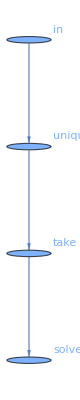

```mathematica
system // First // FFGraphDraw
```

We can now use FiniteFlow to reconstruct the output of the polynomial reduction with ReconstructPolynomialRemainderpaclet:SPQR/ref/ReconstructPolynomialRemainderSPQR Package Symbol

```mathematica
results=ReconstructPolynomialRemainder[system]
```

Generated 18 sample points

Approximate time per evaluation (single core): 6e-06 sec.

{(1/2+(9 a)/2+3 a^2+(49 a^3)/16+a^3 b^2)/a^3+((-3-(117 a)/4-(171 a^2)/8-(7 a^3)/16) y)/a^3+((5/2+36 a+36 a^2+(41 a^3)/16) y^2)/a^3+((-3-(153 a)/4-(315 a^2)/8-(97 a^3)/16) y^3)/a^3+((1/2+(33 a)/2+(27 a^2)/2+(55 a^3)/16) y^4)/a^3+((-9/4-(9 a)/8-(9 a^2)/16) y^5)/a^2,7/2+s-(3 y)/2+y^2/2,9/4-(3 a)/16+(-3+(31 a)/16+a^2/32) y+(9/2-(75 a)/16-(3 a^2)/16) y^2+(-3/4+(95 a)/16+(11 a^2)/32) y^3+(-(45 a)/16-(3 a^2)/16) y^4+((7 a)/16+a^2/32) y^5}

We can check this result against Mathematica's built in functions GroebnerBasis and PolynomialReduce

```mathematica
gb = GroebnerBasis[ideal,variables,CoefficientDomain->RationalFunctions];
ansGB = PolynomialReduce[targets,gb,variables] // Map[Last] // Factor;
ansGB - results // Factor // ContainsOnly[{0}]
```

True

Note how we never needed an explicit Groebner Basis in the computation using SPQR. Only the output of the polynomial division is reconstructed. This is different to Mathematica, where if we don't build a Groebner Basis, the result of the polynomial reduction will not be well defined

```mathematica
ansNoGB = PolynomialReduce[targets,ideal,variables] // Map[Last] // Factor
ansNoGB - results // Factor // ContainsOnly[{0}]
```

{1/(4 a^3)(108-9 a+12 a^3+4 a^3 b^2+72 x+54 a x-120 x^2-36 a x^2-48 x^3-24 a x^3+32 x^4+16 a x^4+54 a y+2 a^3 y-90 a y^2+18 a^2 y^2-6 a^3 y^2+27 a y^3-54 a^2 y^3+2 a^3 y^3+18 a^2 y^4),1/2 (7+2 s-3 y+y^2),x^3}

False

### BuildPolynomialSystempaclet:SPQR/ref/BuildPolynomialSystemSPQR Package Symbol in more detail

Let us examine the output of BuildPolynomialSystempaclet:SPQR/ref/BuildPolynomialSystemSPQR Package Symbol in more detail

```mathematica
system
```

{SPQRGraph$7272,{a,b,s},{DepVars→{targ[1],targ[2],targ[3]},IndepVars→{j[0,5],j[0,4],j[0,3],j[0,2],j[0,1],j[0,0]},SparseOutput→False},{x,y}}

system[[1]] is simply the name of the graph that has been built. system[[2]] is the list of parameters that is eventually reconstructed by FiniteFlow. In system[[3]], DepVars represents the list of the three target polynomials we are reducing.

IndepVars is the most important output, and represents the irreducible monomials that were found by the linear system during row reduction. These are completely analogous to the "master integrals" in an IBP reduction for Feynman integrals. They are indexed by the notation j[a,b] = x^a y^b

Specifically we have

```mathematica
"IndepVars" // ReplaceAll[system[[3]]]//ReplaceAll[j[x__]:>Times@@(variables^{x})]
```

{y^5,y^4,y^3,y^2,y,1}

How do we know if the monomials have been found are correct? We can verify using the command FindIrreducibleMonomialspaclet:SPQR/ref/FindIrreducibleMonomialsSPQR Package Symbol

```mathematica
irreducibleMonomials=FindIrreducibleMonomials[ideal,variables]
```

{y^5,y^4,y^3,y^2,y,1}

These can be passed as an option to BuildPolynomialSystempaclet:SPQR/ref/BuildPolynomialSystemSPQR Package Symbol, which will automatically check if the irreducible monomials found by row reduction agree

If the output is as before, then the check has been passed

```mathematica
system =BuildPolynomialSystem[targets,ideal,variables,maxWeight,"IrreducibleMonomials"->irreducibleMonomials]
```

{SPQRGraph$7321,{a,b,s},{DepVars→{targ[1],targ[2],targ[3]},IndepVars→{j[0,5],j[0,4],j[0,3],j[0,2],j[0,1],j[0,0]},SparseOutput→False},{x,y}}

If we however consider a system with too small of a seed, then in exact analogy to IBPs, the system will not reduce fully

```mathematica
maxWeight = 7;
system =BuildPolynomialSystem[targets,ideal,variables,maxWeight,"IrreducibleMonomials"->irreducibleMonomials]
```

Irreducible monomials do not match. Try increasing the system size

Found 7 monomials: {x^5 y^7,y^5,y^4,y^3,y^2,y,1}

$Failed[7]

BuildPolynomialSystempaclet:SPQR/guide/BuildPolynomialSystem also accepts a min and max weight input, which will automatically increase the seed until either max is reached or the system closes

```mathematica
system =BuildPolynomialSystem[targets,ideal,variables,{1,10},"IrreducibleMonomials"->irreducibleMonomials]
```

system closed at weight: 8

{SPQRGraph$7622,{a,b,s},{DepVars→{targ[1],targ[2],targ[3]},IndepVars→{j[0,5],j[0,4],j[0,3],j[0,2],j[0,1],j[0,0]},SparseOutput→False},{x,y}}

Whenever possible, it is always recommended to precompute the irreducible monomials and to pass them as an option to BuildPolynomialSystempaclet:SPQR/ref/BuildPolynomialSystemSPQR Package Symbol, in order to always insure a correct reduction when reconstruction is performed

### Changing Monomial Ordering

By default, Lexicographic order is used for computing divisions. This can be changed by passing the option "MonomialOrder". It is also possible to ask for verbose output during the construction of the system using "PrintDebugInfo", which accepts the values {0,1,2}.

Define an ideal and a target polynomials to reduce

```mathematica
variables = {x,y};
targets = {a*x^5*y^5*y^2+3+x*y^2+b^2,x*y+s+3,x^3};
ideal = {a*y^2*x^2-2x^2+3,y^2-3y+1-2*x*y};
```

```mathematica
irreducibleMonomials=FindIrreducibleMonomials[ideal,variables,"MonomialOrder"->DegreeReverseLexicographic]
```

{y^3,x^2,y^2,x,y,1}

Build the polynomial system and reconstruct the remainder

```mathematica
maxWeight = 8;
system =BuildPolynomialSystem[targets,ideal,variables,maxWeight,"IrreducibleMonomials"->irreducibleMonomials,"MonomialOrder"->DegreeReverseLexicographic,"PrintDebugInfo"->2]
```

creating system seeds...done: 0.000181s

generating and sorting monomials...done: 0.000898s

preparing to generate system of size 93 x 86...done: 0.000441s

generating system...done: 0.000652s

building FiniteFlow Graph...done: 0.000328s

loading system data into FiniteFlow Graph...done: 0.001063s

learning irreducible monomials...done: 0.000221s

final number of equations needed: 22

{SPQRGraph$7665,{a,b,s},{DepVars→{targ[1],targ[2],targ[3]},IndepVars→{j[0,3],j[2,0],j[0,2],j[1,0],j[0,1],j[0,0]},SparseOutput→False},{x,y}}

```mathematica
results=ReconstructPolynomialRemainder[system, "DeleteGraph" -> False]
```

Generated 21 sample points

Approximate time per evaluation (single core): 1e-05 sec.

{(-6-(45 a)/2-(291 a^2)/4-(9 a^3)/8+3 a^4+a^4 b^2)/a^4+((-9-(9 a)/2-(9 a^2)/4) x)/a^3+((4+24 a+54 a^2+a^3/2) x^2)/a^4+((-18-18 a+(63 a^2)/4+a^3/2) y)/a^3+((24+3 a-(153 a^2)/4-(3 a^3)/2) y^2)/a^3+((-9/2+(9 a)/4+(99 a^2)/8+a^3/2) y^3)/a^3,7/2+s-(3 y)/2+y^2/2,15/8-(3 a)/16+(7/4+a/8) x-(3 x^2)/2+(1/2+(5 a)/8) y+(-3/4-(3 a)/8) y^2+(1/8+a/16) y^3}

Check against built in functions

```mathematica
gb = GroebnerBasis[ideal,variables,CoefficientDomain->RationalFunctions,MonomialOrder->DegreeReverseLexicographic];
ansGB = PolynomialReduce[targets,gb,variables,MonomialOrder->DegreeReverseLexicographic] // Map[Last] // Factor;
ansGB - results // Factor // ContainsOnly[{0}]
```

True

For an exhaustive list of options, see the documentation function page BuildPolynomialSystempaclet:SPQR/ref/BuildPolynomialSystemSPQR Package Symbol

Rational Function Division via Companion Matrices

### Polynomial Division with Companion Matrices

Companion matrices M_x are matrices we can generate from any variable in our system x→ M_x, which encode information on the structure of the ideal, and in particular its polynomial remainders. We delegate further mathematical discussion to manuscript accompanying this package, and here focus on the computational commands.

We define a (single) polynomial we want to reduce, as well as an ideal (list of polynomials) we would like to reduce against

```mathematica
variables = {x,y};
targets ={a*x^5*y^5*y^2+3+x*y^2,x*y^2};
ideal = {a*y^2*x^2-2x^2+3,y^2-3y+1-2*x*y};
```

Precomputing the irreducible monomials is mandatory for building companion matrices

```mathematica
irreducibleMonomials=FindIrreducibleMonomials[ideal,variables]
```

{y^5,y^4,y^3,y^2,y,1}

We can then generate the companion matrices using BuildCompanionMatricespaclet:SPQR/ref/BuildCompanionMatricesSPQR Package Symbol. A companion matrix is generated for each variable (not parameter) in the system, so in this case {x,y}

```mathematica
maxWeight = 4;
cmats = BuildCompanionMatrices[ideal,variables,maxWeight,irreducibleMonomials];
```

The output in the graph can be seen more clearly with

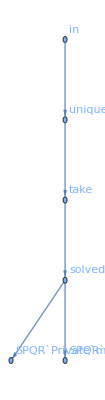

```mathematica
cmats // First // FFGraphDraw
```

The output cmats is very similar to the output produced by BuildPolynomialSystempaclet:SPQR/ref/BuildPolynomialSystemSPQR Package Symbol. Indeed, BuildCompanionMatricespaclet:SPQR/ref/BuildCompanionMatricesSPQR Package Symbol is essentially a wrapper function for BuildPolynomialSystempaclet:SPQR/ref/BuildPolynomialSystemSPQR Package Symbol

```mathematica
cmats
```

{SPQRGraph$7752,{a},{j[0,5],j[0,4],j[0,3],j[0,2],j[0,1],j[0,0]},{SPQR`Private`m[x$11],SPQR`Private`m[y$12]},{x,y}}

If the maxWeight is not large enough, the companion matrix generation will fail, as not all the required polynomials will have been reduced correctly

```mathematica
maxWeight = 3; 
BuildCompanionMatrices[ideal,variables,maxWeight,irreducibleMonomials];
```

Irreducible monomials do not match. Try increasing the system size

Found 8 monomials: {x y^5,y^6,y^5,y^4,y^3,y^2,y,1}

BuildCompanionMatricespaclet:SPQR/ref/BuildCompanionMatricesSPQR Package Symbol also accepts a min and max weight input, which will automatically increase the seed until either max is reached or the system closes

```mathematica
BuildCompanionMatrices[ideal,variables,{1,10},irreducibleMonomials];
```

system closed at weight: 4

The next step in the procedure is to produce a companion matrix for the polynomial we want to reduce. This can be achieved with BuildTargetCompanionMatricespaclet:SPQR/ref/BuildTargetCompanionMatricesSPQR Package Symbol

```mathematica
targetcmats = BuildTargetCompanionMatrices[targets,cmats]
```

{SPQRGraph$7752,{a},{j[0,5],j[0,4],j[0,3],j[0,2],j[0,1],j[0,0]},{SPQR`Private`m[o$15],SPQR`Private`m[o$16]},{x,y}}

This command will parse the expression given in Mathematica and will automatically construct the relevant graph in FiniteFlow

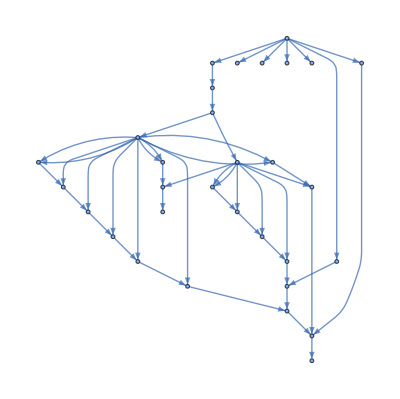

```mathematica
targetcmats // First // FFGraphDraw // FullForm // ReplaceAll[Text[___]:>Text[""]] // Normal // First
```

Finally, we can extract the output of the polynomial division from the target companion matrix, with the command ReconstructTargetCompanionMatricespaclet:SPQR/ref/ReconstructTargetCompanionMatricesSPQR Package Symbol

```mathematica
result = ReconstructTargetCompanionMatrices[targetcmats,"DeleteGraph"->False]
```

{(1/2+(9 a)/2+3 a^2+(49 a^3)/16)/a^3+((-3-(117 a)/4-(171 a^2)/8-(7 a^3)/16) y)/a^3+((5/2+36 a+36 a^2+(41 a^3)/16) y^2)/a^3+((-3-(153 a)/4-(315 a^2)/8-(97 a^3)/16) y^3)/a^3+((1/2+(33 a)/2+(27 a^2)/2+(55 a^3)/16) y^4)/a^3+((-9/4-(9 a)/8-(9 a^2)/16) y^5)/a^2,y/2-(3 y^2)/2+y^3/2}

We can check this result against Mathematica

```mathematica
gb = GroebnerBasis[ideal,variables];
gbAns=PolynomialReduce[targets,gb,variables]//Map[Last]
result - gbAns // Factor // ContainsOnly[#,{0}]&
```

{(8+72 a+48 a^2+49 a^3)/(16 a^3)+((-48-468 a-342 a^2-7 a^3) y)/(16 a^3)+((40+576 a+576 a^2+41 a^3) y^2)/(16 a^3)+((-48-612 a-630 a^2-97 a^3) y^3)/(16 a^3)+((8+264 a+216 a^2+55 a^3) y^4)/(16 a^3)-(9 (4+2 a+a^2) y^5)/(16 a^2),y/2-(3 y^2)/2+y^3/2}

True

By default, Lexicographic order is used for computing divisions. This can be changed by passing the option "MonomialOrder" to BuildCompanionMatricespaclet:SPQR/ref/BuildCompanionMatricesSPQR Package Symbol , in a manner identical to BuildPolynomialSystempaclet:SPQR/ref/BuildPolynomialSystemSPQR Package Symbol. Make sure to also pass the same option to FindIrreducibleMonomialspaclet:SPQR/ref/FindIrreducibleMonomialsSPQR Package Symbol! Likewise the option "PrintDebugInfo" will output progress on intermediate computations

For more examples and options, see also the function documentation page of ReconstructTargetCompanionMatricespaclet:SPQR/ref/ReconstructTargetCompanionMatricesSPQR Package Symbol

### Rational Function Division with Companion Matrices

Companion matrices allow us to also construct the polynomial remainders  of rational functions, not just polynomials. The parsing and building of the rational functions is automatically handled by BuildTargetCompanionMatricespaclet:SPQR/ref/BuildTargetCompanionMatricesSPQR Package Symbol, and can handle nested rational expressions to arbitrary depth

We define a rational function

```mathematica
ratFunc = (a+x+1/y)/((x/(y-3)+y^2)^2)
```

(a+x+1/y)/((x/(-3+y)+y^2)^2)

and build the companion matrix

```mathematica
ratFunccmat = BuildTargetCompanionMatrices[{ratFunc},cmats]
```

{SPQRGraph$7752,{a},{j[0,5],j[0,4],j[0,3],j[0,2],j[0,1],j[0,0]},{SPQR`Private`m[o$17]},{x,y}}

This output is now added to the previous graph

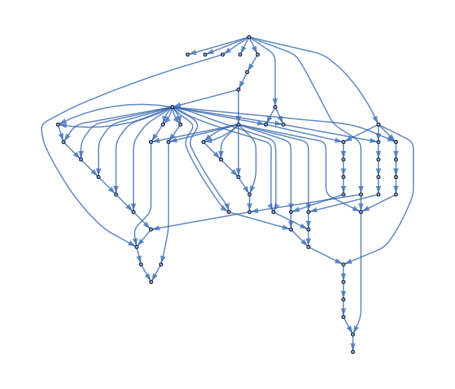

```mathematica
ratFunccmat // First // FFGraphDraw // FullForm // ReplaceAll[Text[___]:>Text[""]] // Normal // First
```

Finally the output is reconstructed as usual with

```mathematica
ratFuncResult = ReconstructTargetCompanionMatrices[ratFunccmat]//First;
ratFuncResult // Collect[#,{x,y},Factor]&
```

-((-27934368000-61047574784 a-54369569760 a^2-25113305072 a^3-6352725849 a^4-854413450 a^5-53804282 a^6-1086999 a^7+10974 a^8)/(24880+25688 a+7571 a^2+451 a^3+a^4)^2)+((-20201480960-40653889536 a-36166472096 a^2-17900355312 a^3-5148677755 a^4-813853223 a^5-54325143 a^6-708114 a^7+35484 a^8) y)/(24880+25688 a+7571 a^2+451 a^3+a^4)^2+((58769210880+108331397888 a+78627302208 a^2+20834044928 a^3-3761837826 a^4-3255847679 a^5-616192192 a^6-44350818 a^7-930735 a^8+11046 a^9) y^2)/(2 (24880+25688 a+7571 a^2+451 a^3+a^4)^2)-((10097592320-27819160320 a-88517951488 a^2-92415688608 a^3-48235698488 a^4-13067454835 a^5-1716098481 a^6-98929311 a^7-1490046 a^8+35046 a^9) y^3)/(2 (24880+25688 a+7571 a^2+451 a^3+a^4)^2)+(a (-29384605440-65408368384 a-61601574688 a^2-30343497664 a^3-7896692159 a^4-1003233493 a^5-55815959 a^6-756830 a^7+21938 a^8) y^4)/(2 (24880+25688 a+7571 a^2+451 a^3+a^4)^2)-(a (-5048796160-11337548800 a-10690409344 a^2-5247189584 a^3-1357444684 a^4-171022025 a^5-9396845 a^6-121081 a^7+3882 a^8) y^5)/(2 (24880+25688 a+7571 a^2+451 a^3+a^4)^2)

Mathematica does not support multivariate polynomial division of rational functions. However, it is at least possible to check that the result is correct with the following code

```mathematica
PolynomialReduce[ratFuncResult*(ratFunc//Together//Denominator),gb,variables][[2]]//Factor;
PolynomialReduce[(ratFunc//Together//Numerator),gb,variables][[2]]//Factor;
%==%%//Factor
```

True

Elimination Theory

SPQR provides functionality for eliminating variables from polynomial ideals. The package provides two distinct ways to do this, one using companion matrices, and a second more traditional approach using elimination orderings. The companion matrix approach has the advantage that it works for any monomial ordering, often resulting in lighter computations.

### Characteristic Polynomials of Companion Matrices

We set up a polynomial system

```mathematica
variables = {x,y,z};
ideal = {b+x^2-y+z^2*y+a,a+x^2*z+y*z+c*z^2,a+z+x*y^2+x*y^3z+3+c}; 
ideal // MatrixForm
```

(a+b+x^2-y+y z^2
a+x^2 z+y z+c z^2
3+a+c+x y^2+z+x y^3 z)

Suppose we want to eliminate {x,y} from this system. With Mathematica we can use GroebnerBasis or Eliminate. This may take a few minutes to run

```mathematica
elim=GroebnerBasis[ideal,{z},{x,y},CoefficientDomain->RationalFunctions]//First//Factor; // AbsoluteTiming
elim // Short
```

{39.3056,Null}

-4 a^5+4 a^6-a^7+12 a^5 z-16 a^6 z+5 a^7 z+12 a^4 b z-16 a^5 b z+«836»+a^2 z^19+6 c z^19+2 a c z^19+c^2 z^19+6 z^20+2 a z^20+2 c z^20+z^21

It can be shown that elim is related to the characteristic polynomial of the companion matrix M_z. To this end, SPQR provides functionality for computing characteristic polynomials with finite fields.

For elimination via characteristic polynomials, the order of the variables does not matter. We thus first begin by (optionally) sorting the variables using SortVariablespaclet:SPQR/ref/SortVariablesSPQR Package Symbol.  This command will try find an ordering which results in a simpler Macaulay matrix

```mathematica
variablesSorted = SortVariables[ideal,variables,"MonomialOrder"->DegreeReverseLexicographic]
```

{x,z,y}

We proceed by building the companion matrices for the system. The characteristic polynomial is unique no matter the monomial ordering, so we suggest DegreeReverseLexicographic

```mathematica
irreds = FindIrreducibleMonomials[ideal,variablesSorted,"MonomialOrder"->DegreeReverseLexicographic];
cmats = BuildCompanionMatrices[ideal,variablesSorted,{1,10},irreds,"MonomialOrder"->DegreeReverseLexicographic]
```

system closed at weight: 6

{SPQRGraph$10070,{a,b,c},{j[1,0,3],j[0,1,3],j[0,0,4],j[3,0,0],j[1,2,0],j[0,3,0],j[2,0,1],j[1,1,1],j[1,0,2],j[0,1,2],j[0,0,3],j[2,0,0],j[1,1,0],j[0,2,0],j[1,0,1],j[0,1,1],j[0,0,2],j[1,0,0],j[0,1,0],j[0,0,1],j[0,0,0]},{SPQR`Private`m[x$18],SPQR`Private`m[z$19],SPQR`Private`m[y$20]},{x,z,y}}

We then build the characteristic polynomial for z, with the command BuildCharacteristicPolynomialspaclet:SPQR/ref/BuildCharacteristicPolynomialsSPQR Package Symbol. The second option instructs the function to only build the characteristic polynomial for z (the 2nd variable after sorting)

```mathematica
charp = BuildCharacteristicPolynomials[cmats,{2}]
```

{SPQRGraph$10070,{a,b,c},{j[1,0,3],j[0,1,3],j[0,0,4],j[3,0,0],j[1,2,0],j[0,3,0],j[2,0,1],j[1,1,1],j[1,0,2],j[0,1,2],j[0,0,3],j[2,0,0],j[1,1,0],j[0,2,0],j[1,0,1],j[0,1,1],j[0,0,2],j[1,0,0],j[0,1,0],j[0,0,1],j[0,0,0]},{SPQR`Private`char$10084[z$19]}}

BuildCharacteristicPolynomialspaclet:SPQR/ref/BuildCharacteristicPolynomialsSPQR Package Symbol implements the Faddeev–LeVerrier algorithm to build each coefficient sequentially. This can be seen by viewing the newly appended FiniteFlow graph

```mathematica
charp // First // FFGraphDraw // FullForm // ReplaceAll[Text[___]:>Text[""]] // Normal // First
```

Finally the result can be reconstructed with the ReconstructCharacteristicPolynomialspaclet:SPQR/ref/ReconstructCharacteristicPolynomialsSPQR Package Symbol

```mathematica
rec = ReconstructCharacteristicPolynomials[charp]//First; // AbsoluteTiming
```

Generated 122 sample points

Approximate time per evaluation (single core): 0.000607 sec.

{0.013499,Null}

The characteristic polynomial can then be built by dotting each element of the output list with its respective power of z

```mathematica
elimRec=irreds//Length//Range[0,#]&//Power[z,#]&//Dot[#,rec]&//Factor//Numerator; // AbsoluteTiming
```

{0.006262,Null}

Check against Mathematica

```mathematica
elimRec/elim//Factor
```

-1

### Elimination Ordering

For a more traditional approach to eliminating variables, the function BuildPolynoimalSystem supports Elimination orderings, which we describe below

First, we find on a numerical slice the elimination polynomial and its degree

```mathematica
elimN = GroebnerBasis[ideal//ReplaceAll[{a,b,c}->RandomInteger[100,3]//Thread],{z},{x,y},CoefficientDomain->RationalFunctions]//First; // AbsoluteTiming
elimN
degree = elimN //Exponent[#,z]&
```

{0.005479,Null}

-8589935940111+67925194607871 z-250398630817662 z^2+533537092955769 z^3-616252728291743 z^4-11832751378908 z^5+1607750353633815 z^6-3774905855434175 z^7+5656966770456450 z^8-6532543223453261 z^9+6180174860628607 z^10-4850819659096296 z^11+3098161080151884 z^12-1542253272354544 z^13+558986585356128 z^14-131167396515400 z^15+15033129979504 z^16-314916 z^17-4200 z^18+22486 z^19+300 z^20+z^21

21

We then compute the irreducible monomials appearing as

```mathematica
irreds=FindIrreducibleMonomials[elimN,{z}]
```

{z^20,z^19,z^18,z^17,z^16,z^15,z^14,z^13,z^12,z^11,z^10,z^9,z^8,z^7,z^6,z^5,z^4,z^3,z^2,z,1}

We then set up a polynomial system to reduce z^degree. We pass the option "EliminateVariables" to BuildPolynomialSystempaclet:SPQR/ref/BuildPolynomialSystemSPQR Package Symbol to sort the monomials in a way that removes {x,y} from the system. The option "MonomialOrder" specifies the ordering used inside the various elimination blocks. We recommend using DegreeReverseLexicographic. We note that as usual a high enough weight must be supplied for the system to close correctly

```mathematica
BuildPolynomialSystem[{z^degree},ideal,variables,22,"IrreducibleMonomials"->irreds,"MonomialOrder"->DegreeReverseLexicographic,"EliminateVariables"->{{x,y},0},"PrintDebugInfo"->2];//AbsoluteTiming
```

creating system seeds...done: 0.005766s

generating and sorting monomials...done: 0.064907s

preparing to generate system of size 6901 x 3799...done: 0.018617s

generating system...done: 0.065183s

building FiniteFlow Graph...done: 0.000352s

loading system data into FiniteFlow Graph...done: 0.073002s

learning irreducible monomials...done: 0.009266s

final number of equations needed: 279

{0.255934,Null}

The "EliminateVariables" option accepts a list with two entries. The first is a list of variables to be eliminated. The second input is a number, which represents (an optional) value to truncate  the system in the variables to be eliminated. 

If the truncation is too large the system will not close:

```mathematica
BuildPolynomialSystem[{z^degree},ideal,variables,22,"IrreducibleMonomials"->irreds,"MonomialOrder"->DegreeReverseLexicographic,"EliminateVariables"->{{x,y},20}]; // AbsoluteTiming
```

Irreducible monomials do not match. Try increasing the system size

Found 1 monomials: {z^21}

{0.032397,Null}

Often however one can get away with a significantly smaller system by truncating to an appropriate degree

```mathematica
system=BuildPolynomialSystem[{z^degree},ideal,variables,22,"IrreducibleMonomials"->irreds,"MonomialOrder"->DegreeReverseLexicographic,"EliminateVariables"->{{x,y},19},"PrintDebugInfo"->2]; // AbsoluteTiming
```

creating system seeds...done: 0.004915s

generating and sorting monomials...done: 0.007016s

preparing to generate system of size 631 x 626...done: 0.001978s

generating system...done: 0.005236s

building FiniteFlow Graph...done: 0.000301s

loading system data into FiniteFlow Graph...done: 0.007092s

learning irreducible monomials...done: 0.002367s

final number of equations needed: 279

{0.031632,Null}

We can now reconstruct the result of the polynomial division

```mathematica
remainder = ReconstructPolynomialRemainder[system]//First; // AbsoluteTiming
```

Generated 122 sample points

Approximate time per evaluation (single core): 0.000125 sec.

{0.0105,Null}

And build the full elimination polynomial as

```mathematica
elimRec=z^degree - remainder // Together // Numerator // Factor; // AbsoluteTiming
elimRec//Short
```

{0.012191,Null}

-4 a^5+4 a^6-a^7+12 a^5 z-16 a^6 z+5 a^7 z+12 a^4 b z-16 a^5 b z+«836»+a^2 z^19+6 c z^19+2 a c z^19+c^2 z^19+6 z^20+2 a z^20+2 c z^20+z^21

Checking the result

```mathematica
elimRec/elim//Factor
```

1

List of Various Examples

Benchmarks

| Related Guides
▪SPQR